```mathematica
(*Question No 1a*)
```

```mathematica
setA=Range[3]
```

{1,2,3}

```mathematica
(*Question No 1b*)
```

```mathematica
setB=Select[Range[12],OddQ]
```

{1,3,5,7,9,11}

```mathematica
(*Question No 1c*)
```

```mathematica
setC=Select[Fibonacci[Range[20]],#<1000&&PrimeQ[#]&]
```

{2,3,5,13,89,233}

```mathematica
(*Qusestion No 2a*)
```

```mathematica
MemberQ[{1,3,5,7},3]
```

True

```mathematica
(*Question No 2b*)
```

```mathematica
MemberQ[{2,4,6,8},6]
```

True

```mathematica
(*Question No 2c*)
```

```mathematica
MemberQ[Range[16],10]
```

True

```mathematica
(*Question No 2d*)
```

```mathematica
Not[MemberQ[Range[16],11]]
```

False

```mathematica
(*Question No 2e*)
```

```mathematica
Not[MemberQ[Select[Range[10],EvenQ],4]]
```

False

```mathematica
Exit[]
```

```mathematica
(*Question No 03*)
```

```mathematica
a[x_,y_]:=(x^2+y^2=1);
b[x_,y_]:=((x-1.3)^2+y^2=1);
c[x_,y_]:=((x-1.3)^2+(y-0.75)^2=1);
```

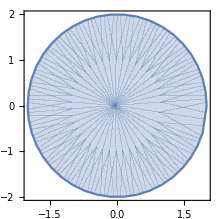

```mathematica
RegionPlot[Disk[{0,0},2]]
```

```mathematica
Clear[C]
```

Clear::wrsym: Symbol C is Protected.

```mathematica
setA=Disk[{0,0},2];
setB=Disk[{0,1},2];
setC=Disk[{1,1},2];
```

```mathematica
(*a*)
```

```mathematica
RegionPlot[setA]
```

-Graphics-

```mathematica
(*b*)
```

```mathematica
RegionPlot[{setA&&setB}]
```

RegionPlot::argr: RegionPlot called with 1 argument; 3 arguments are expected.

RegionPlot[{setA&&setB}]

```mathematica
Exit[]
```

```mathematica
(*Question No 04*)
```

```mathematica
setA={c};
setB={a,b};
setC={b,d};
setU={a,b,c,d,e,f};
```

```mathematica
(*A U (B' U C')*)
```

```mathematica
Union[setA,Intersection[Complement[setU,setB],Complement[setU,setC]]]
```

{c,e,f}

```mathematica
(*(A U B') ^ (A ^ C')*)
```

```mathematica
Intersection[Union[setA,Complement[setU,setB]],Union[setA,Complement[setU,setC]]]
```

{c,e,f}

```mathematica
Exit[]
```

```mathematica
(*Questoin No 05*)
```

```mathematica
setA={1,3,4,5,6};
setB={2,4,7,8};
setU={1,2,3,4,5,6,7,8,9,11};
```

```mathematica
LHS=Complement[setU,Union[setA,setB]]
RHS=Intersection[Complement[setU,setA],Complement[setU,setB]]
```

{9,11}

{9,11}

```mathematica
(*Question No 06*)
```

```mathematica
d=150;
m=140;
s=120;
dm=60;
ds=50;
ms=40;
dms=25;
total=300;
```

```mathematica
(*a*)
```

```mathematica
exactly1=(d-dm-ds+dms)+(m-dm-ms+dms)+(s-ds-ms+dms)
```

185

```mathematica
(*b*)
```

```mathematica
exactly2=(dm-dms)+(ds-dms)+(ms-dms)
```

75

```mathematica
(*c*)
```

```mathematica
atleast1=exactly1+exactly2+dms
```

210

```mathematica
(*d*)
```

```mathematica
none=total-atleast1
```

90

```mathematica
(*Question No 07*)
```

```mathematica
c[m_]:=Piecewise[{{0.5m,m<=100},{50+0.3m,100<m<=300},{110+0.2m,m>300}}];
avg[m_]:=c[m]/m;
```

```mathematica
c[80]
avg[80]
```

40.

0.5

```mathematica
c[150]
avg[150]
```

95.

0.633333

```mathematica
c[450]
avg[450]
```

200.

0.444444

```mathematica
Exit[]
```

```mathematica
(*question no 03*)
```

```mathematica
cirA[x_,y_]:=x^2+y^2=1
cirB[x_,y_]:=(x-1.3)^2+y^2=1
cirC[x_,y_]:=(x-1.3)^2+(y-0.75)^2=1
(*a*)
```

```mathematica
RegionPlot[{cirA[x,y]},{x,-1,-3},{y,-1,-3}]
```

Set::write: Tag Plus in x^2+y^2 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

-Graphics-